# Stochastic Differential Equations with Mathematica

## About the author

Author : Nelson Mok
email : madeinquant@gmail.com

### Summary

The Mathematica versions in Higham “An Algorithmic Introduction to Numerical Simulation of Stochastic Differential Equations”, SIAM Review, Vol. 43, No. 3, 2001.

The Details can be found in the paper (http://www.caam.rice.edu/~cox/stoch/dhigham.pdf)

## Brownian Motion (bpath1.m)

```mathematica
xj = Table[Random[Integer,{0,1}],{10}];
```

```mathematica
wij = Table[Random[Real,{-0.5,0.5}],{10}];
```

```mathematica
neti = xj.wij
```

0.0719003

## bpath2

```mathematica
xj = Table[Random[Integer,{0,1}],{10}];
```

```mathematica
wij = Table[Random[Real,{-0.5,0.5}],{10}];
```

```mathematica
neti = xj.wij
```

0.0719003

## Simulated Annealing

Plotting f(t) shows that this function has many local minima.
http://stackoverflow.com/questions/19757551/basics-of-simulated-annealing-in-python
http://cboard.cprogramming.com/cplusplus-programming/162080-simulated-annealing-algorithm-cplusplus.html

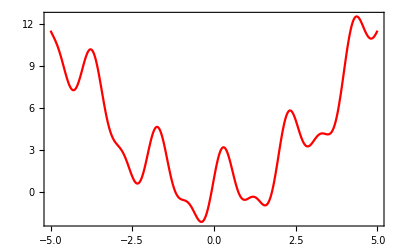

```mathematica
f[x_]=0.5 x^2+Cos[Pi x]2 Sin[Pi x]+Cos[Pi x]+2Sin[ Pi x];
plt1=Plot[f[x],{x,-5,5},PlotStyle-> RGBColor[1,0,0],Frame-> True]
```

Using built-in functions of Mathematica

```mathematica
NMinimize[f[x],{x, -5,5}]
```

{-2.10466,{x→-0.386468}}

```mathematica
fTmp = fBest = xBest= xTmp= 999.0;
k = 0;
LIMIT = 10^6;
tTmp = tInit = 300;
Delta=0.999999;
```

```mathematica
For [tTmp = Delta * tTmp;,k<LIMIT,k++,
xTmp= RandomReal[{-5,5}];
fTmp = f[xTmp];
If [fTmp<fBest,fBest = fTmp;xBest = xTmp,
PRA = N[Min[{1,Exp[-(fTmp-fBest)/tTmp]}]];
R = RandomReal[{0.0,1.0}];
(*If [R<PRA,fBest = fTmp;xBest = xTmp;k++,];*)
];
(*Delta= N[(LIMIT+1-k)/LIMIT];*)
tTmp = Delta * tTmp;
(* Print[tTmp]*)
];
Print[xBest]
Print[fBest]
```

-0.386458

-2.10466

## The Traveling Salesperson Problen (TSP)

### Number of Pathes

```mathematica
numTours[n_] := n!/( 2 n)
```

```mathematica
numTours[10]
```

181440

### Cost of Traveling

```mathematica
costs= Table[If[i≤j,0,Random[Integer,{1,10}]],{i,5},{j,5}];
costs = costs + Transpose[costs];
MatrixForm[costs]
```

(0 | 6 | 9 | 6 | 4
6 | 0 | 7 | 10 | 3
9 | 7 | 0 | 2 | 9
6 | 10 | 2 | 0 | 3
4 | 3 | 9 | 3 | 0)

181440

```mathematica
neti = xj.wij
```

0.0719003

## Logistic Classifier

### http://aimotion.blogspot.hk/2011/11/machine-learning-with-python-logistic.html

```mathematica
<<CUDALink`
CUDAResourcesInstall[Update->True]
```

{Paclet[CUDAResources,10.2.0.3,<>]}

```mathematica
Needs["CUDALink`"]
CUDAInformation[]
```

CUDAInformation::legcy: CUDA is no longer supported on {}. Refer to CUDALink System Requirements for system requirements.

CUDAInformation[]

```mathematica
Needs["OpenCLLink`"]
OpenCLQ[]
OpenCLInformation[1,2,"Type"]
```

True

GPU

```mathematica
OpenCLMemoryLoad[ConstantArray[0,10]]
OpenCLMemoryInformation[%]
```

OpenCLMemory[<958519787>,Integer64]

{ID→958519787,HostStatus→Synchronized,DeviceStatus→Uninitialized,Residence→DeviceHost,Sharing→Cloned,Type→Integer64,ByteCount→80,Dimensions→{10},Platform→1,Device→2,MathematicaType→List,TypeInformation→{}}

```mathematica
Needs["OpenCLLink`"]
{width,height}={512,512};
jset=OpenCLMemoryAllocate[Real,{height,width}];
JuliaCalculate=OpenCLFunctionLoad[code,"julia_kernel",{{_Real,_,"Output"},_Integer,_Integer, _Real, _Real},{16,16},"Defines"->{"MAX_ITERATIONS"->10,"ZOOM_LEVEL"->"0.0050","BAILOUT"->"4.0"}];
```

OpenCLFunctionLoad::invprog: OpenCLLink encountered an invalid program.

```mathematica
Needs["RLink`"]
InstallR["RHomeLocation"->"/usr/local/Cellar/r/3.2.4_1/R.framework/Resources","RVersion"->3 ](*for M 10.0.1*)
REvaluate["R.Version()"]
```

RObject[{{x86_64-apple-darwin15.3.0},{x86_64},{darwin15.3.0},{x86_64, darwin15.3.0},{Revised},{3},{2.4},{2016},{03},{16},{70336},{R},{R version 3.2.4 Revised (2016-03-16 r70336)},{Very Secure Dishes}},RAttributes[names:>{platform,arch,os,system,status,major,minor,year,month,day,svn rev,language,version.string,nickname}]]

## Logistic Classifier

### http://aimotion.blogspot.hk/2011/11/machine-learning-with-python-logistic.html http://bbs.pinggu.org/forum.php?mod=collection&action=view&ctid=2624

```mathematica
scores={3.0,1.0,0.2}
```

{3.,1.,0.2}

```mathematica
r_x= REvaluate["{
	3 + 4 # Calculate 3 + 4
	6 + 12 # Calculate 6 + 12
}"]
```

{18.}

```mathematica
REvaluate["{
	# Import the training set:train
	train_url<-\"http://s3.amazonaws.com/assets.datacamp.com/course/Kaggle/train.csv\"
train<-read.csv(file=train_url,head=TRUE,sep=\",\")

# Import the testing set:test
test_url<-\"http://s3.amazonaws.com/assets.datacamp.com/course/Kaggle/test.csv\"
test<-read.csv(file=test_url,head=TRUE,sep=\",\")

# Print train and test to the console
train
test
}"]
```

REvaluate::rerr: Failed to retrieve the value for variable or piece of code {
	# Import the training set:train
	train_url<-"http://s3.amazon…RUE,sep=",")

# Print train and test to the console
train
test
}. The following R error was encountered: Error in file(file, "rt") : cannot open the connection

$Failed